## Electroweakino tensors

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of two packages found in the “include” folder.

```mathematica
description = "Computation of the electroweakino tensors in factorised partonic neutralino pair production.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts", "FeynHelpers"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Successfully patched FeynArts.

```mathematica
$EwinoRoot = ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$EwinoRoot, "include"}]];
<< XSec`
<< EWinos`

FCClearScalarProducts[];
```

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{$EwinoRoot, "results", "LO"}];
```

## Generate Feynman diagram and amplitude

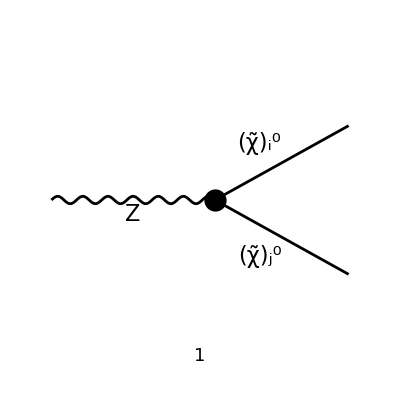

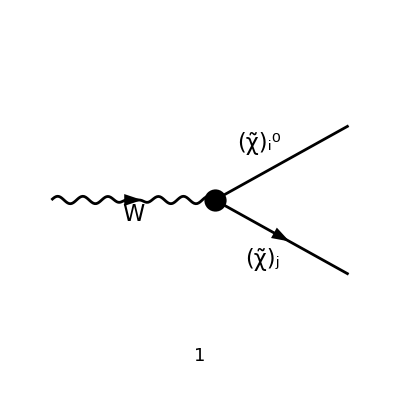

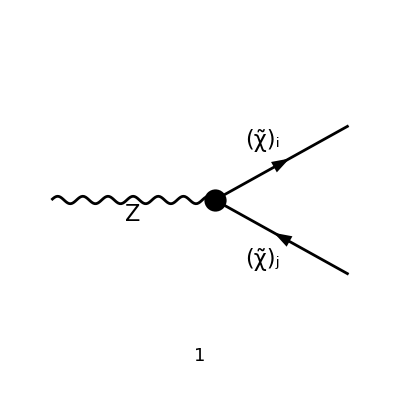

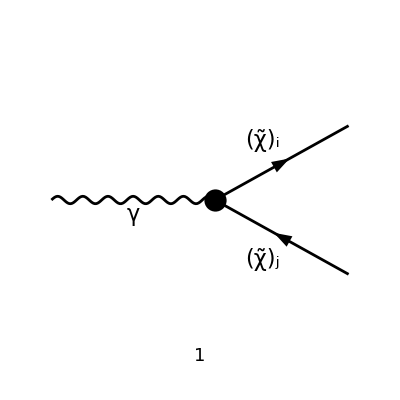

```mathematica
NNdiag = InsertFields[
	CreateTopologies[0, 1 -> 2], 
	{V[2]} -> {F[11, {i}], F[11, {j}]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}
];
Paint[NNdiag, Numbering->Simple, ColumnsXRows -> {1, 1}, ImageSize->{512,256}];

NCdiag = InsertFields[
	CreateTopologies[0, 1 -> 2], 
	{V[3]} -> {F[11, {i}], F[12, {j}]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}
];
Paint[NCdiag, Numbering->Simple, ColumnsXRows -> {1, 1}, ImageSize->{512,256}];

CCdiagZ = InsertFields[
	CreateTopologies[0, 1 -> 2], 
	{V[2]} -> {F[12, {i}], -F[12, {j}]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}
];
Paint[CCdiagZ, Numbering->Simple, ColumnsXRows -> {1, 1}, ImageSize->{512,256}];
CCdiagA = InsertFields[
	CreateTopologies[0, 1 -> 2], 
	{V[1]} -> {F[12, {i}], -F[12, {j}]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}
];
Paint[CCdiagA, Numbering->Simple, ColumnsXRows -> {1, 1}, ImageSize->{512,256}];
```

```mathematica
amp[0] = FCFAConvert[
	CreateFeynAmp[NNdiag], 
	IncomingMomenta -> {q},
	OutgoingMomenta -> {pi, pj},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,D],Momentum[Polarization[q,ⅈ],D]] -> FAD[{q, Sqrt[DZ]}];
NCamp[0] = FCFAConvert[
	CreateFeynAmp[NCdiag], 
	IncomingMomenta -> {q},
	OutgoingMomenta -> {pi, pj},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,D],Momentum[Polarization[q,ⅈ],D]] -> FAD[{q, Sqrt[DW]}];
CCampZ[0] = (FCFAConvert[
	CreateFeynAmp[CCdiagZ], 
	IncomingMomenta -> {q},
	OutgoingMomenta -> {pi, pj},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,D],Momentum[Polarization[q,ⅈ],D]] -> FAD[{q, Sqrt[DZ]}]);

CCampA[0] = FCFAConvert[
	CreateFeynAmp[CCdiagA], 
	IncomingMomenta -> {q},
	OutgoingMomenta -> {pi, pj},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,D],Momentum[Polarization[q,ⅈ],D]] -> FAD[q];
```

```mathematica
amp[1] = amp[0] /. ZSimplifyRules // ChangeDimension[#, 4]&
NCamp[1] = NCamp[0] /. WSimplifyRules // ChangeDimension[#, 4]&
CCampZ[1] = CCampZ[0] /. ASimplifyRules /. FeynCalc`IndexDelta[j,i] -> FeynCalc`IndexDelta[i,j] // ChangeDimension[#, 4]&
CCampA[1] = CCampA[0] /. ASimplifyRules /. FeynCalc`IndexDelta[j,i] -> FeynCalc`IndexDelta[i,j] // ChangeDimension[#, 4]&
```

-(ⅈ (φ(OverBar[p_j],m_j)).(-ⅈ g_W (γ̄)^μ.(γ̄)^6 O_ij^(′′L)-ⅈ g_W (γ̄)^μ.(γ̄)^7 O_ij^(′′R)).(φ(-OverBar[p_i],m_i)))/((q̄)^2-Δ_Z)

-(ⅈ (φ(OverBar[p_j],m_j)).(-ⅈ g_W (γ̄)^μ.(γ̄)^6 O_ij^L-ⅈ g_W (γ̄)^μ.(γ̄)^7 O_ij^R).(φ(-OverBar[p_i],m_i)))/((q̄)^2-Δ_W)

(ⅈ (φ(OverBar[p_i],m_i)).(ⅈ g_W (γ̄)^μ.(γ̄)^6 O_ji^(′L)+ⅈ g_W (γ̄)^μ.(γ̄)^7 O_ji^(′R)).(φ(-OverBar[p_j],m_j)))/((q̄)^2-Δ_Z)

(ⅈ (φ(OverBar[p_i],m_i)).(ⅈ g_W (γ̄)^μ δ_ij (sin(θ_W))).(φ(-OverBar[p_j],m_j)))/(q̄)^2

```mathematica
ampD[1] = amp[0] /. ZSimplifyRules;
NCampD[1] = NCamp[0] /. WSimplifyRules;
CCampZD[1] = CCampZ[0] /. ASimplifyRules /. FeynCalc`IndexDelta[j,i] -> FeynCalc`IndexDelta[i,j];
CCampAD[1] = CCampA[0];
```

## Set scalar products

```mathematica
SP[pi, pi] = MEW[i]^2;
SP[pj, pj] = MEW[j]^2;
SP[pi, pj] = (Q2-MEW[i]^2-MEW[j]^2)/2;
SP[q, pi] = (Q2+MEW[i]^2-MEW[j]^2)/2;
SP[q, pj] = (Q2-MEW[i]^2+MEW[j]^2)/2;
SP[q, q] = Q2;
SPD[pi, pi] = MEW[i]^2;
SPD[pj, pj] = MEW[j]^2;
SPD[pi, pj] = (Q2-MEW[i]^2-MEW[j]^2)/2;
SPD[q, pi] = (Q2+MEW[i]^2-MEW[j]^2)/2;
SPD[q, pj] = (Q2-MEW[i]^2+MEW[j]^2)/2;
SPD[q, q] = Q2;
```

## Evaluate square amplitudes

Square the amplitude and simplify sum over fermion chains

```mathematica
NNTensor[0] = amp[1] (ConjugateAmplitude[amp[1]/.μ->ν]) // FermionSpinSum // DiracSimplify
```

-(2 g_W^2 m_i m_j (ḡ)^μν O_ij^(′′L) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(2 g_W^2 m_i m_j (ḡ)^μν O_ij^(′′R) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_i^2 (ḡ)^μν O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_j^2 (ḡ)^μν O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 OverBar[p_i]^ν OverBar[p_j]^μ O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 OverBar[p_i]^μ OverBar[p_j]^ν O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+-(2 ⅈ g_W^2 O_ij^(′′L) (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(Q2 g_W^2 (ḡ)^μν O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_i^2 (ḡ)^μν O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_j^2 (ḡ)^μν O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 OverBar[p_i]^ν OverBar[p_j]^μ O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 OverBar[p_i]^μ OverBar[p_j]^ν O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 ⅈ g_W^2 O_ij^(′′R) (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(Q2 g_W^2 (ḡ)^μν O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))

```mathematica
NNTensorD[0] = ampD[1] (ConjugateAmplitude[ampD[1]/.μ->ν]) // FermionSpinSum // DiracSimplify // SelectFree2[#, DiracTrace]&
```

-(2 g_W^2 m_i m_j g^μν O_ij^(′′L) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(2 g_W^2 m_i m_j g^μν O_ij^(′′R) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_i^2 g^μν O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_j^2 g^μν O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 p_i^ν p_j^μ O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 p_i^μ p_j^ν O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(Q2 g_W^2 g^μν O_ij^(′′L) Conjugate[(O_ij^(′′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_i^2 g^μν O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_j^2 g^μν O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 p_i^ν p_j^μ O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 p_i^μ p_j^ν O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(Q2 g_W^2 g^μν O_ij^(′′R) Conjugate[(O_ij^(′′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))

```mathematica
NCTensor[0] = NCamp[1] ( ConjugateAmplitude[NCamp[1] /. μ -> ν]) // FermionSpinSum // DiracSimplify
```

-(2 g_W^2 m_i m_j (ḡ)^μν O_ij^L Conjugate[(O_ij^R)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))-(2 g_W^2 m_i m_j (ḡ)^μν O_ij^R Conjugate[(O_ij^L)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(g_W^2 m_i^2 (ḡ)^μν O_ij^L Conjugate[(O_ij^L)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(g_W^2 m_j^2 (ḡ)^μν O_ij^L Conjugate[(O_ij^L)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(2 g_W^2 OverBar[p_i]^ν OverBar[p_j]^μ O_ij^L Conjugate[(O_ij^L)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(2 g_W^2 OverBar[p_i]^μ OverBar[p_j]^ν O_ij^L Conjugate[(O_ij^L)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+-(2 ⅈ g_W^2 O_ij^L Conjugate[(O_ij^L)] (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]))/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))-(Q2 g_W^2 (ḡ)^μν O_ij^L Conjugate[(O_ij^L)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(g_W^2 m_i^2 (ḡ)^μν O_ij^R Conjugate[(O_ij^R)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(g_W^2 m_j^2 (ḡ)^μν O_ij^R Conjugate[(O_ij^R)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(2 g_W^2 OverBar[p_i]^ν OverBar[p_j]^μ O_ij^R Conjugate[(O_ij^R)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(2 g_W^2 OverBar[p_i]^μ OverBar[p_j]^ν O_ij^R Conjugate[(O_ij^R)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))+(2 ⅈ g_W^2 O_ij^R Conjugate[(O_ij^R)] (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]))/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))-(Q2 g_W^2 (ḡ)^μν O_ij^R Conjugate[(O_ij^R)])/((Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))

```mathematica
CCZTensor[0] = CCampZ[1] (ConjugateAmplitude[CCampZ[1]/.μ->ν]) // FermionSpinSum // DiracSimplify
```

-(2 g_W^2 m_i m_j (ḡ)^μν O_ji^(′L) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(2 g_W^2 m_i m_j (ḡ)^μν O_ji^(′R) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_i^2 (ḡ)^μν O_ji^(′L) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_j^2 (ḡ)^μν O_ji^(′L) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 OverBar[p_i]^ν OverBar[p_j]^μ O_ji^(′L) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 OverBar[p_i]^μ OverBar[p_j]^ν O_ji^(′L) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 ⅈ g_W^2 O_ji^(′L) (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(Q2 g_W^2 (ḡ)^μν O_ji^(′L) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_i^2 (ḡ)^μν O_ji^(′R) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 m_j^2 (ḡ)^μν O_ji^(′R) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 OverBar[p_i]^ν OverBar[p_j]^μ O_ji^(′R) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(2 g_W^2 OverBar[p_i]^μ OverBar[p_j]^ν O_ji^(′R) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(2 ⅈ g_W^2 O_ji^(′R) (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))-(Q2 g_W^2 (ḡ)^μν O_ji^(′R) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))

```mathematica
CCATensor[0] = (CCampA[0] ConjugateAmplitude[CCampA[0]/.μ->ν]) // FermionSpinSum // DiracSimplify
```

2 (1/Q2)^2 g_W^2 m_i^2 g^μν δ_ij^2 (sin(θ_W))^2+2 (1/Q2)^2 g_W^2 m_j^2 g^μν δ_ij^2 (sin(θ_W))^2-4 (1/Q2)^2 g_W^2 m_i m_j g^μν δ_ij^2 (sin(θ_W))^2+4 (1/Q2)^2 g_W^2 p_i^ν p_j^μ δ_ij^2 (sin(θ_W))^2+4 (1/Q2)^2 g_W^2 p_i^μ p_j^ν δ_ij^2 (sin(θ_W))^2-2 Q2 (1/Q2)^2 g_W^2 g^μν δ_ij^2 (sin(θ_W))^2

```mathematica
CCAZTensor[0] = CCampA[1] (ConjugateAmplitude[CCampZ[1]/.μ->ν]) + (CCampZ[1]/.μ->ν) (ConjugateAmplitude[CCampA[1]]) // FermionSpinSum // DiracSimplify
```

(2 ⅈ Conjugate[(O_ji^(′L))] (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]) δ_ij g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))-(2 ⅈ Conjugate[(O_ji^(′R))] (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]) δ_ij g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))-(2 ⅈ (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]) δ_ij O_ji^(′L) g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(2 ⅈ (ϵ̄)^(μν OverBar[p_i]OverBar[p_j]) δ_ij O_ji^(′R) g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(Conjugate[(O_ji^(′L))] δ_ij m_i^2 (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))+(Conjugate[(O_ji^(′R))] δ_ij m_i^2 (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))+(Conjugate[(O_ji^(′L))] δ_ij m_j^2 (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))+(Conjugate[(O_ji^(′R))] δ_ij m_j^2 (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))-(Q2 Conjugate[(O_ji^(′L))] δ_ij (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))-(Q2 Conjugate[(O_ji^(′R))] δ_ij (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))-(2 Conjugate[(O_ji^(′L))] δ_ij m_i m_j (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))-(2 Conjugate[(O_ji^(′R))] δ_ij m_i m_j (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))+(δ_ij m_i^2 O_ji^(′L) (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(δ_ij m_j^2 O_ji^(′L) (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))-(Q2 δ_ij O_ji^(′L) (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))-(2 δ_ij m_i m_j O_ji^(′L) (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(δ_ij m_i^2 O_ji^(′R) (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(δ_ij m_j^2 O_ji^(′R) (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))-(Q2 δ_ij O_ji^(′R) (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))-(2 δ_ij m_i m_j O_ji^(′R) (ḡ)^μν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(2 Conjugate[(O_ji^(′L))] δ_ij OverBar[p_j]^μ OverBar[p_i]^ν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))+(2 Conjugate[(O_ji^(′R))] δ_ij OverBar[p_j]^μ OverBar[p_i]^ν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))+(2 δ_ij O_ji^(′L) OverBar[p_j]^μ OverBar[p_i]^ν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(2 δ_ij O_ji^(′R) OverBar[p_j]^μ OverBar[p_i]^ν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(2 Conjugate[(O_ji^(′L))] δ_ij OverBar[p_i]^μ OverBar[p_j]^ν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))+(2 Conjugate[(O_ji^(′R))] δ_ij OverBar[p_i]^μ OverBar[p_j]^ν g_W^2 (sin(θ_W)))/(Q2 (Q2-Conjugate[(Δ_Z)]))+(2 δ_ij O_ji^(′L) OverBar[p_i]^μ OverBar[p_j]^ν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))+(2 δ_ij O_ji^(′R) OverBar[p_i]^μ OverBar[p_j]^ν g_W^2 (sin(θ_W)))/(Q2 (Q2-Δ_Z))

## Phase space factor

Setting up some assumptions.

```mathematica
$Assumptions = {
	Q2 ∈ PositiveReals,
	MEW[_] ∈ PositiveReals,
	MCha[_] ∈ PositiveReals,
	Q2 >= (MEW[i]+MEW[j])^2,
	p ∈ PositiveReals,
	Epsilon ∈ Reals,
	EpsilonUV ∈ NegativeReals,
	EpsilonIR ∈ PositiveReals,
	SMP[_] ∈ Reals,
	alphaW ∈ Reals,
	EulerGamma ∈ PositiveReals,
	CF ∈ Reals,
	CA ∈ Reals,
	IdenticalPartFactor[__] ∈ PositiveReals
};
```

There are two kinds of kinetic terms that are dubbed K1[Q2] and K2[Q2].

```mathematica
MakeBoxes[K1, TraditionalForm] = SubscriptBox["K", 1];
MakeBoxes[K2, TraditionalForm] = SubscriptBox["K", 2];
KineticTermShorthands = {
	MEW[i]^4:> -12K1[Q2] - MEW[i]^2(Q2-2MEW[j]^2) - Q2 MEW[j]^2 - MEW[j]^4 + 2Q2^2,
	MEW[i] MEW[j] :> K2[Q2]/Q2};
```

The common phase space factor.

```mathematica
PiNeu = p/(4Pi Sqrt[Q2]);
```

Knowing that we can write N^μν = N_1 g^μν + N_2 (q^μ q^ν)/Q2, we can find the coefficients using the following contractions.

### Neutralino pair production

```mathematica
NN1 = 1/3(Pair[LorentzIndex[μ], LorentzIndex[ν]] - (Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)NNTensor[0] //
	Contract // DiracSimplify // Simplify
NN2 = 1/3(-Pair[LorentzIndex[μ], LorentzIndex[ν]] + 4(Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)NNTensor[0] //
	Contract // DiracSimplify // Simplify
```

(g_W^2 (Conjugate[(O_ij^(′′L))] ((m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′L)-6 Q2 m_i m_j O_ij^(′′R))+Conjugate[(O_ij^(′′R))] (-6 Q2 m_i m_j O_ij^(′′L)+(Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′R)+m_i^2 (Q2-2 m_j^2) O_ij^(′′R)+m_i^4 O_ij^(′′R))))/(3 Q2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))

(2 g_W^2 (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ij^(′′L) Conjugate[(O_ij^(′′L))]+O_ij^(′′R) Conjugate[(O_ij^(′′R))]))/(3 Q2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))

Setting up the neutralino tensor  (in  dimensions).

```mathematica
NNTensor[1] = PiNeu (Pair[LorentzIndex[μ], LorentzIndex[ν]] NN1 + (Pair[LorentzIndex[μ], Momentum[q]]Pair[LorentzIndex[ν], Momentum[q]])/Q2 NN2)
```

(p ((2 g_W^2 (q̄)^μ (q̄)^ν (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ij^(′′L) Conjugate[(O_ij^(′′L))]+O_ij^(′′R) Conjugate[(O_ij^(′′R))]))/(3 Q2^2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 (ḡ)^μν (Conjugate[(O_ij^(′′L))] ((m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′L)-6 Q2 m_i m_j O_ij^(′′R))+Conjugate[(O_ij^(′′R))] (-6 Q2 m_i m_j O_ij^(′′L)+(Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′R)+m_i^2 (Q2-2 m_j^2) O_ij^(′′R)+m_i^4 O_ij^(′′R))))/(3 Q2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))))/(4 π √Q2)

```mathematica
Export[FileNameJoin[{ResultsDir, "NNTensor.m"}], NNTensor[1] // FullForm // ToString];
```

Now to extract the K[1] and K[2] coefficients of the  -term.

```mathematica
NN1subbed = NN1 /. KineticTermShorthands // Collect2[#, {K[1], K[2]}]&
```

-(2 g_W^2 (K_2(Q2) O_ij^(′′L) Conjugate[(O_ij^(′′R))]+K_2(Q2) O_ij^(′′R) Conjugate[(O_ij^(′′L))]+2 K_1(Q2) O_ij^(′′L) Conjugate[(O_ij^(′′L))]+2 K_1(Q2) O_ij^(′′R) Conjugate[(O_ij^(′′R))]))/(Q2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))

Then write the coefficients to file.

```mathematica
Export[FileNameJoin[{ResultsDir, "NNcoeffs.m"}], {Coefficient[NN1subbed, K1[Q2]], Coefficient[NN1subbed, K2[Q2]]} // FullForm // ToString];
```

### Neutralino-Chargino production

Knowing that we can write N^μν = N_1 g^μν + N_2 (q^μ q^ν)/Q2, we can find the coefficients using the following contractions.

```mathematica
NC1 = 1/3(Pair[LorentzIndex[μ], LorentzIndex[ν]] - (Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)NCTensor[0] //
	Contract // DiracSimplify // Simplify
NC2 = 1/3(-Pair[LorentzIndex[μ], LorentzIndex[ν]] + 4(Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)NCTensor[0] //
	Contract // DiracSimplify // Simplify
```

(g_W^2 (Conjugate[(O_ij^L)] (O_ij^L (m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2)-6 Q2 m_i m_j O_ij^R)+Conjugate[(O_ij^R)] (-6 Q2 m_i m_j O_ij^L+(Q2 m_j^2+m_j^4-2 Q2^2) O_ij^R+m_i^2 (Q2-2 m_j^2) O_ij^R+m_i^4 O_ij^R)))/(3 Q2 (Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))

(2 g_W^2 (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ij^L Conjugate[(O_ij^L)]+O_ij^R Conjugate[(O_ij^R)]))/(3 Q2 (Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))

Setting up a function to get the neutralino tensor with given Lorentz index names (in  dimensions).

```mathematica
NCTensor[1] = PiNeu (Pair[LorentzIndex[μ], LorentzIndex[ν]] NC1 + (Pair[LorentzIndex[μ], Momentum[q]]Pair[LorentzIndex[ν], Momentum[q]])/Q2 NC2);
```

```mathematica
Export[FileNameJoin[{ResultsDir, "NCTensor.m"}], NCTensor[1] // FullForm // ToString];
```

Now to extract the K1[Q2] and K2[Q2] coefficients of the  -term.

```mathematica
NC1subbed = NC1 /. KineticTermShorthands // Collect2[#, {K1[Q2], K2[Q2]}]&
```

-(2 g_W^2 K_2(Q2) (O_ij^L Conjugate[(O_ij^R)]+O_ij^R Conjugate[(O_ij^L)]))/(Q2 (Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))-(4 g_W^2 K_1(Q2) (O_ij^L Conjugate[(O_ij^L)]+O_ij^R Conjugate[(O_ij^R)]))/(Q2 (Q2-Δ_W) (Q2-Conjugate[(Δ_W)]))

Then write the coefficients to file.

```mathematica
Export[FileNameJoin[{ResultsDir, "NCcoeffs.m"}], {Coefficient[NC1subbed, K1[Q2]], Coefficient[NC1subbed, K2[Q2]]} // FullForm // ToString];
```

### Chargino pair production

Knowing that we can write C^μν = C_1 g^μν + C_2 (q^μ q^ν)/Q2, we can find the coefficients using the following contractions.

```mathematica
CCZ1 = 1/3(Pair[LorentzIndex[μ], LorentzIndex[ν]] - (Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)CCZTensor[0] //
	Contract // DiracSimplify // Simplify
CCZ2 = 1/3(-Pair[LorentzIndex[μ], LorentzIndex[ν]] + 4(Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)CCZTensor[0] //
	Contract // DiracSimplify // Simplify
CCA1 = 1/3(Pair[LorentzIndex[μ], LorentzIndex[ν]] - (Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)CCATensor[0] //
	Contract // DiracSimplify // Simplify
CCA2 = 1/3(-Pair[LorentzIndex[μ], LorentzIndex[ν]] + 4(Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)CCATensor[0] //
	Contract // DiracSimplify // Simplify
CCAZ1 = 1/3(Pair[LorentzIndex[μ], LorentzIndex[ν]] - (Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)CCAZTensor[0] //
	Contract // DiracSimplify // Simplify
CCAZ2 = 1/3(-Pair[LorentzIndex[μ], LorentzIndex[ν]] + 4(Pair[LorentzIndex[μ],Momentum[q]]Pair[LorentzIndex[ν],Momentum[q]])/Q2)CCAZTensor[0] //
	Contract // DiracSimplify // Simplify
```

(g_W^2 (Conjugate[(O_ji^(′L))] ((m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2) O_ji^(′L)-6 Q2 m_i m_j O_ji^(′R))+Conjugate[(O_ji^(′R))] (-6 Q2 m_i m_j O_ji^(′L)+(Q2 m_j^2+m_j^4-2 Q2^2) O_ji^(′R)+m_i^2 (Q2-2 m_j^2) O_ji^(′R)+m_i^4 O_ji^(′R))))/(3 Q2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))

(2 g_W^2 (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ji^(′L) Conjugate[(O_ji^(′L))]+O_ji^(′R) Conjugate[(O_ji^(′R))]))/(3 Q2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))

(2 (1/Q2)^2 g_W^2 δ_ij^2 (sin(θ_W))^2 (m_i^2 (Q2-2 m_j^2)-6 Q2 m_i m_j+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2))/(3 Q2)

(4 (1/Q2)^2 g_W^2 δ_ij^2 (sin(θ_W))^2 (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2))/(3 Q2)

-(g_W^2 δ_ij (sin(θ_W)) (-m_i^2 (Q2-2 m_j^2)+6 Q2 m_i m_j-m_i^4-Q2 m_j^2-m_j^4+2 Q2^2) (Conjugate[(O_ji^(′L))]/(Q2-Conjugate[(Δ_Z)])+Conjugate[(O_ji^(′R))]/(Q2-Conjugate[(Δ_Z)])+(O_ji^(′L)+O_ji^(′R))/(Q2-Δ_Z)))/(3 Q2 Q2)

(2 g_W^2 δ_ij (sin(θ_W)) (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (Conjugate[(O_ji^(′L))]/(Q2-Conjugate[(Δ_Z)])+Conjugate[(O_ji^(′R))]/(Q2-Conjugate[(Δ_Z)])+(O_ji^(′L)+O_ji^(′R))/(Q2-Δ_Z)))/(3 Q2 Q2)

Setting up a function to get the chargino tensor with given Lorentz index names (in  dimensions).

```mathematica
CCZTensor[1] = PiNeu (Pair[LorentzIndex[μ], LorentzIndex[ν]] CCZ1 + (Pair[LorentzIndex[μ], Momentum[q]]Pair[LorentzIndex[ν], Momentum[q]])/Q2 CCZ2);
CCATensor[1] = PiNeu (Pair[LorentzIndex[μ], LorentzIndex[ν]] CCA1 + (Pair[LorentzIndex[μ], Momentum[q]]Pair[LorentzIndex[ν], Momentum[q]])/Q2 CCA2);
CCAZTensor[1] = PiNeu (Pair[LorentzIndex[μ], LorentzIndex[ν]] CCAZ1 + (Pair[LorentzIndex[μ], Momentum[q]]Pair[LorentzIndex[ν], Momentum[q]])/Q2 CCAZ2);
```

```mathematica
Export[FileNameJoin[{ResultsDir, "CCTensor.m"}], CCZTensor[1] +CCATensor[1] +CCAZTensor[1] // FullForm // ToString];
```

Now to extract the K1[Q2] and K2[Q2] coefficients of the  -term.

```mathematica
CC1subbed = CCZ1+CCA1+CCAZ1 /. KineticTermShorthands // Collect2[#, {K1[Q2], K2[Q2]}, Factoring -> Factor2]& // FeynAmpDenominatorExplicit
```

-(2 g_W^2 K_2(Q2) ((O_ji^(′L) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(O_ji^(′R) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(δ_ij (sin(θ_W)) Conjugate[(O_ji^(′L))])/(Q2 (Q2-Conjugate[(Δ_Z)]))+(δ_ij (sin(θ_W)) Conjugate[(O_ji^(′R))])/(Q2 (Q2-Conjugate[(Δ_Z)]))+(δ_ij (sin(θ_W)) O_ji^(′L))/(Q2 (Q2-Δ_Z))+(δ_ij (sin(θ_W)) O_ji^(′R))/(Q2 (Q2-Δ_Z))+(2 δ_ij^2 (sin(θ_W))^2)/Q2^2))/Q2-(4 g_W^2 K_1(Q2) ((δ_ij (sin(θ_W)) Conjugate[(O_ji^(′L))])/(Q2 (Q2-Conjugate[(Δ_Z)]))+(O_ji^(′L) Conjugate[(O_ji^(′L))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(δ_ij (sin(θ_W)) Conjugate[(O_ji^(′R))])/(Q2 (Q2-Conjugate[(Δ_Z)]))+(O_ji^(′R) Conjugate[(O_ji^(′R))])/((Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(δ_ij (sin(θ_W)) O_ji^(′L))/(Q2 (Q2-Δ_Z))+(δ_ij (sin(θ_W)) O_ji^(′R))/(Q2 (Q2-Δ_Z))+(2 δ_ij^2 (sin(θ_W))^2)/Q2^2))/Q2

Then write the coefficients to file.

```mathematica
Export[FileNameJoin[{ResultsDir, "CCcoeffs.m"}], {Coefficient[CC1subbed, K1[Q2]], Coefficient[CC1subbed, K2[Q2]]} // FullForm // ToString];
```